```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final-CPK-Messing-Around/Ratesfunc.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

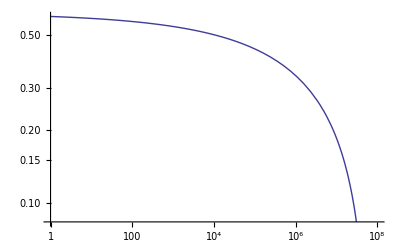

```mathematica
LogLogPlot[ϵMu,{M,1,10^8}]
```

```mathematica
NSolve[(f0*M^γ+mm0*M^ζ)/M==1,M]
```

{{M→6.53794×10^7}}

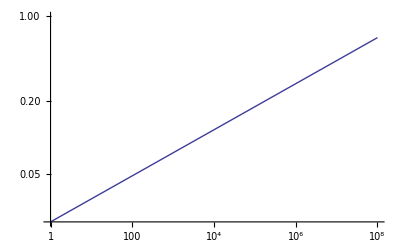

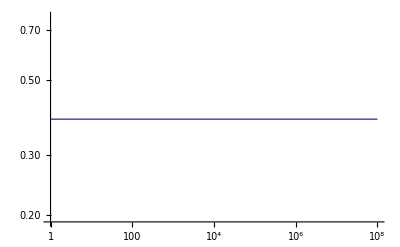

```mathematica
LogLogPlot[(f0*M^γ)/M,{M,1,10^8}]
LogLogPlot[(mm0*M^ζ)/M,{M,1,10^8}]
```

```mathematica
mm0*M^ζ
```

0.383 M^1.

```mathematica
mm0
```

0.383

```mathematica
Rstar =RSS;
Hstar =HSS;
Fstar = FSS;
StarRates={Rstar,Hstar,Fstar}/.{λ->ConsumerGrowth,μ->Mortality,β->FullMaintenance,δ->StarveMaintenance,α->ResourceGrowth,σ->Starvation,ρ->Recovery};
dimR = dimRSS[StarRates[[1]]];
dimH = dimSS[StarRates[[2]]];
dimF = dimSS[StarRates[[3]]];
```

```mathematica
Fstar
```

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

```mathematica
Fstar/.{μ->0}
(2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ)/.{μ->0}
```

0

4 δ λ^3 ρ^2

```mathematica
FullSimplify[Hstar/Fstar]
```

λ/μ

```mathematica
α λ μ^2 (μ+2 ρ) (σ-λ)/.{λ->ConsumerGrowth,μ->Mortality,β->FullMaintenance,δ->StarveMaintenance,α->ResourceGrowth,σ->Starvation,ρ->Recovery}
```

-(1.33296×10^-14 ((1.41054×10^-6)/(M^(1/4) Log[0.0127415/(1-0.558031/M^0.02)])-(6.71429×10^-6)/(M^(1/4) Log[1-0.0202 M^0.19])) (-(3.35714×10^-6)/(M^(1/4) Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))])+1/(148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M])))/(M^(1/4) Log[0.0127415/(1-0.558031/M^0.02)] (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M])^2)

```mathematica
(2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ)/.{λ->ConsumerGrowth,μ->Mortality,β->FullMaintenance,δ->StarveMaintenance,α->ResourceGrowth,σ->Starvation,ρ->Recovery}
```

((4.7354×10^-12)/(√M Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))] Log[0.0127415/(1-0.558031/M^0.02)])-(6.71429×10^-6)/(M^(1/4) Log[1-0.0202 M^0.19] (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))) (-(6.71429×10^-6 (-1/(M^(1/4) Log[0.0127415/(1-0.558031/M^0.02)])1.41054×10^-6 (-(1.67857×10^-6)/(M^(1/4) Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))])+(5.73866×10^-7 ((1-0.0202 M^0.19) M)^(3/4))/((1-0.0202 M^0.19) M^(1/4) (2.63558×10^-8 (1/(1-0.558031/M^0.02))^4. (-0.290908 M^0.92+(-(2.32051×10^7 (-1+0.558031/M^0.02))/((1/(1-0.558031/M^0.02))^3.)-(221750. (-1+0.558031/M^0.02)^2)/((1/(1-0.558031/M^0.02))^2.)-(1255.74 (-1+0.558031/M^0.02)^3)/((1/(1-0.558031/M^0.02))^1.)+3 (-1+0.695081/M^0.06-1.86839/M^0.04+2.23213/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.558031/M^0.02)])/((1/(1-0.558031/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^4. (0.290908 M^0.92+(3 (1-0.695081/M^0.06+1.86839/M^0.04-2.23213/M^0.02)+(48 (-1+0.558031/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^3.)+(36 (-1+0.558031/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^2.)+(16 (-1+0.558031/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^4.)))))+(0.22222 M^(3/4) ((2.58242×10^-6)/M^(1/4)-1/(M Log[0.0127415/(1-0.558031/M^0.02)])8.36467×10^-14 (1/(1-0.558031/M^0.02))^4. (0.290908 (-1+(3.79423×10^7)/((1/(1-0.558031/M^0.02))^4.)) M^0.92+(-(2.32051×10^7 (-1+0.558031/M^0.02))/((1/(1-0.558031/M^0.02))^3.)-(221750. (-1+0.558031/M^0.02)^2)/((1/(1-0.558031/M^0.02))^2.)-(1255.74 (-1+0.558031/M^0.02)^3)/((1/(1-0.558031/M^0.02))^1.)+3 (-1+0.695081/M^0.06-1.86839/M^0.04+2.23213/M^0.02)+(3.79423×10^7 (-25+0.695081/M^0.06+1.86839/M^0.04+6.69638/M^0.02))/((1/(1-0.558031/M^0.02))^4.)) M-(4.55308×10^8 M Log[0.0127415/(1-0.558031/M^0.02)])/((1/(1-0.558031/M^0.02))^4.))))/((2.63558×10^-8 (1/(1-0.558031/M^0.02))^4. (-0.290908 M^0.92+(-(2.32051×10^7 (-1+0.558031/M^0.02))/((1/(1-0.558031/M^0.02))^3.)-(221750. (-1+0.558031/M^0.02)^2)/((1/(1-0.558031/M^0.02))^2.)-(1255.74 (-1+0.558031/M^0.02)^3)/((1/(1-0.558031/M^0.02))^1.)+3 (-1+0.695081/M^0.06-1.86839/M^0.04+2.23213/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.558031/M^0.02)])/((1/(1-0.558031/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^4. (0.290908 M^0.92+(3 (1-0.695081/M^0.06+1.86839/M^0.04-2.23213/M^0.02)+(48 (-1+0.558031/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^3.)+(36 (-1+0.558031/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^2.)+(16 (-1+0.558031/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^4.))) (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))))/(M^(1/4) Log[1-0.0202 M^0.19] (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))+1/(√M Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))] Log[0.0127415/(1-0.558031/M^0.02)])2.3677×10^-12 (-(1.61893×10^-12 ((1-0.0202 M^0.19) M)^(3/4))/((1-0.0202 M^0.19) √M Log[0.0127415/(1-0.558031/M^0.02)] (2.63558×10^-8 (1/(1-0.558031/M^0.02))^4. (-0.290908 M^0.92+(-(2.32051×10^7 (-1+0.558031/M^0.02))/((1/(1-0.558031/M^0.02))^3.)-(221750. (-1+0.558031/M^0.02)^2)/((1/(1-0.558031/M^0.02))^2.)-(1255.74 (-1+0.558031/M^0.02)^3)/((1/(1-0.558031/M^0.02))^1.)+3 (-1+0.695081/M^0.06-1.86839/M^0.04+2.23213/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.558031/M^0.02)])/((1/(1-0.558031/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^4. (0.290908 M^0.92+(3 (1-0.695081/M^0.06+1.86839/M^0.04-2.23213/M^0.02)+(48 (-1+0.558031/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^3.)+(36 (-1+0.558031/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^2.)+(16 (-1+0.558031/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^4.))))+(1.41054×10^-6)/(M^(1/4) Log[0.0127415/(1-0.558031/M^0.02)] (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))+(0.444441 M^(3/4) ((2.58242×10^-6)/M^(1/4)-1/(M Log[0.0127415/(1-0.558031/M^0.02)])8.36467×10^-14 (1/(1-0.558031/M^0.02))^4. (0.290908 (-1+(3.79423×10^7)/((1/(1-0.558031/M^0.02))^4.)) M^0.92+(-(2.32051×10^7 (-1+0.558031/M^0.02))/((1/(1-0.558031/M^0.02))^3.)-(221750. (-1+0.558031/M^0.02)^2)/((1/(1-0.558031/M^0.02))^2.)-(1255.74 (-1+0.558031/M^0.02)^3)/((1/(1-0.558031/M^0.02))^1.)+3 (-1+0.695081/M^0.06-1.86839/M^0.04+2.23213/M^0.02)+(3.79423×10^7 (-25+0.695081/M^0.06+1.86839/M^0.04+6.69638/M^0.02))/((1/(1-0.558031/M^0.02))^4.)) M-(4.55308×10^8 M Log[0.0127415/(1-0.558031/M^0.02)])/((1/(1-0.558031/M^0.02))^4.))))/((2.63558×10^-8 (1/(1-0.558031/M^0.02))^4. (-0.290908 M^0.92+(-(2.32051×10^7 (-1+0.558031/M^0.02))/((1/(1-0.558031/M^0.02))^3.)-(221750. (-1+0.558031/M^0.02)^2)/((1/(1-0.558031/M^0.02))^2.)-(1255.74 (-1+0.558031/M^0.02)^3)/((1/(1-0.558031/M^0.02))^1.)+3 (-1+0.695081/M^0.06-1.86839/M^0.04+2.23213/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.558031/M^0.02)])/((1/(1-0.558031/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^4. (0.290908 M^0.92+(3 (1-0.695081/M^0.06+1.86839/M^0.04-2.23213/M^0.02)+(48 (-1+0.558031/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^3.)+(36 (-1+0.558031/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^2.)+(16 (-1+0.558031/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.558031/M^0.02))^4.))) (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))))

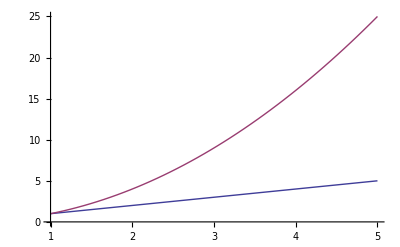

```mathematica
Plot[{x,x^2},{x,1,5}]
```

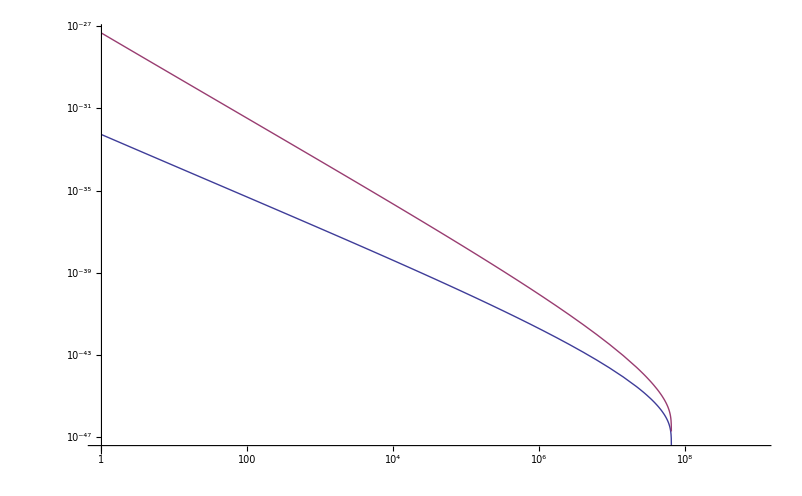

```mathematica
LogLogPlot[{-(1.3329638043197945*^-14 ((1.4105437082749147*^-6)/(M^(1/4) Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)])-(6.714285714285714*^-6)/(M^(1/4) Log[1-0.0202 M^0.18999999999999995])) (-(3.357142857142857*^-6)/(M^(1/4) Log[0.012741455098566168/(1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))])+1/(148936.17021276595 M^(1/4) Log[1-0.0202 M^0.18999999999999995]-148936.17021276595 M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M])))/(M^(1/4) Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)] (148936.17021276595 M^(1/4) Log[1-0.0202 M^0.18999999999999995]-148936.17021276595 M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M])^2),((4.735396734922928*^-12)/(√M Log[0.012741455098566168/(1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))] Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)])-(6.714285714285714*^-6)/(M^(1/4) Log[1-0.0202 M^0.18999999999999995] (148936.17021276595 M^(1/4) Log[1-0.0202 M^0.18999999999999995]-148936.17021276595 M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))) (-(6.714285714285714*^-6 (-1/(M^(1/4) Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)])1.4105437082749147*^-6 (-(1.6785714285714286*^-6)/(M^(1/4) Log[0.012741455098566168/(1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))])+(5.738656044336681*^-7 ((1-0.0202 M^0.18999999999999995) M)^(3/4))/((1-0.0202 M^0.18999999999999995) M^(1/4) (2.6355794484267528*^-8 (1/(1-0.5580312878153593/M^0.01999999999999999))^4. (-0.29090785873264535 M^0.92+(-(2.320513787191087*^7 (-1+0.5580312878153593/M^0.01999999999999999))/((1/(1-0.5580312878153593/M^0.01999999999999999))^3.)-(221750.41668824226 (-1+0.5580312878153593/M^0.01999999999999999)^2)/((1/(1-0.5580312878153593/M^0.01999999999999999))^2.)-(1255.743545476256 (-1+0.5580312878153593/M^0.01999999999999999)^3)/((1/(1-0.5580312878153593/M^0.01999999999999999))^1.)+3 (-1+0.6950813573471186/M^0.05999999999999997-1.8683935090852102/M^0.03999999999999998+2.232125151261437/M^0.01999999999999999)) M-(4.553078453834172*^8 M Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)])/((1/(1-0.5580312878153593/M^0.01999999999999999))^4.))+((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^4. (0.29090785873264535 M^0.92+(3 (1-0.6950813573471186/M^0.05999999999999997+1.8683935090852102/M^0.03999999999999998-2.232125151261437/M^0.01999999999999999)+(48 (-1+0.5580312878153593/M^0.01999999999999999))/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^3.)+(36 (-1+0.5580312878153593/M^0.01999999999999999)^2)/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^2.)+(16 (-1+0.5580312878153593/M^0.01999999999999999)^3)/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^1.)) M+(12. M Log[(1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999)])/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^4.)))))+(0.22222029788708003 M^(3/4) ((2.5824175824175822*^-6)/M^(1/4)-1/(M Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)])8.364672453382506*^-14 (1/(1-0.5580312878153593/M^0.01999999999999999))^4. (0.29090785873264535 (-1+(3.79423204486181*^7)/((1/(1-0.5580312878153593/M^0.01999999999999999))^4.)) M^0.92+(-(2.320513787191087*^7 (-1+0.5580312878153593/M^0.01999999999999999))/((1/(1-0.5580312878153593/M^0.01999999999999999))^3.)-(221750.41668824226 (-1+0.5580312878153593/M^0.01999999999999999)^2)/((1/(1-0.5580312878153593/M^0.01999999999999999))^2.)-(1255.743545476256 (-1+0.5580312878153593/M^0.01999999999999999)^3)/((1/(1-0.5580312878153593/M^0.01999999999999999))^1.)+3 (-1+0.6950813573471186/M^0.05999999999999997-1.8683935090852102/M^0.03999999999999998+2.232125151261437/M^0.01999999999999999)+(3.79423204486181*^7 (-25+0.6950813573471186/M^0.05999999999999997+1.8683935090852102/M^0.03999999999999998+6.696375453784311/M^0.01999999999999999))/((1/(1-0.5580312878153593/M^0.01999999999999999))^4.)) M-(4.553078453834172*^8 M Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)])/((1/(1-0.5580312878153593/M^0.01999999999999999))^4.))))/((2.6355794484267528*^-8 (1/(1-0.5580312878153593/M^0.01999999999999999))^4. (-0.29090785873264535 M^0.92+(-(2.320513787191087*^7 (-1+0.5580312878153593/M^0.01999999999999999))/((1/(1-0.5580312878153593/M^0.01999999999999999))^3.)-(221750.41668824226 (-1+0.5580312878153593/M^0.01999999999999999)^2)/((1/(1-0.5580312878153593/M^0.01999999999999999))^2.)-(1255.743545476256 (-1+0.5580312878153593/M^0.01999999999999999)^3)/((1/(1-0.5580312878153593/M^0.01999999999999999))^1.)+3 (-1+0.6950813573471186/M^0.05999999999999997-1.8683935090852102/M^0.03999999999999998+2.232125151261437/M^0.01999999999999999)) M-(4.553078453834172*^8 M Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)])/((1/(1-0.5580312878153593/M^0.01999999999999999))^4.))+((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^4. (0.29090785873264535 M^0.92+(3 (1-0.6950813573471186/M^0.05999999999999997+1.8683935090852102/M^0.03999999999999998-2.232125151261437/M^0.01999999999999999)+(48 (-1+0.5580312878153593/M^0.01999999999999999))/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^3.)+(36 (-1+0.5580312878153593/M^0.01999999999999999)^2)/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^2.)+(16 (-1+0.5580312878153593/M^0.01999999999999999)^3)/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^1.)) M+(12. M Log[(1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999)])/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^4.))) (148936.17021276595 M^(1/4) Log[1-0.0202 M^0.18999999999999995]-148936.17021276595 M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))))/(M^(1/4) Log[1-0.0202 M^0.18999999999999995] (148936.17021276595 M^(1/4) Log[1-0.0202 M^0.18999999999999995]-148936.17021276595 M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))+1/(√M Log[0.012741455098566168/(1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))] Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)])2.367698367461464*^-12 (-(1.6189250354585833*^-12 ((1-0.0202 M^0.18999999999999995) M)^(3/4))/((1-0.0202 M^0.18999999999999995) √M Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)] (2.6355794484267528*^-8 (1/(1-0.5580312878153593/M^0.01999999999999999))^4. (-0.29090785873264535 M^0.92+(-(2.320513787191087*^7 (-1+0.5580312878153593/M^0.01999999999999999))/((1/(1-0.5580312878153593/M^0.01999999999999999))^3.)-(221750.41668824226 (-1+0.5580312878153593/M^0.01999999999999999)^2)/((1/(1-0.5580312878153593/M^0.01999999999999999))^2.)-(1255.743545476256 (-1+0.5580312878153593/M^0.01999999999999999)^3)/((1/(1-0.5580312878153593/M^0.01999999999999999))^1.)+3 (-1+0.6950813573471186/M^0.05999999999999997-1.8683935090852102/M^0.03999999999999998+2.232125151261437/M^0.01999999999999999)) M-(4.553078453834172*^8 M Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)])/((1/(1-0.5580312878153593/M^0.01999999999999999))^4.))+((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^4. (0.29090785873264535 M^0.92+(3 (1-0.6950813573471186/M^0.05999999999999997+1.8683935090852102/M^0.03999999999999998-2.232125151261437/M^0.01999999999999999)+(48 (-1+0.5580312878153593/M^0.01999999999999999))/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^3.)+(36 (-1+0.5580312878153593/M^0.01999999999999999)^2)/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^2.)+(16 (-1+0.5580312878153593/M^0.01999999999999999)^3)/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^1.)) M+(12. M Log[(1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999)])/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^4.))))+(1.4105437082749147*^-6)/(M^(1/4) Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)] (148936.17021276595 M^(1/4) Log[1-0.0202 M^0.18999999999999995]-148936.17021276595 M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))+(0.44444059577416006 M^(3/4) ((2.5824175824175822*^-6)/M^(1/4)-1/(M Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)])8.364672453382506*^-14 (1/(1-0.5580312878153593/M^0.01999999999999999))^4. (0.29090785873264535 (-1+(3.79423204486181*^7)/((1/(1-0.5580312878153593/M^0.01999999999999999))^4.)) M^0.92+(-(2.320513787191087*^7 (-1+0.5580312878153593/M^0.01999999999999999))/((1/(1-0.5580312878153593/M^0.01999999999999999))^3.)-(221750.41668824226 (-1+0.5580312878153593/M^0.01999999999999999)^2)/((1/(1-0.5580312878153593/M^0.01999999999999999))^2.)-(1255.743545476256 (-1+0.5580312878153593/M^0.01999999999999999)^3)/((1/(1-0.5580312878153593/M^0.01999999999999999))^1.)+3 (-1+0.6950813573471186/M^0.05999999999999997-1.8683935090852102/M^0.03999999999999998+2.232125151261437/M^0.01999999999999999)+(3.79423204486181*^7 (-25+0.6950813573471186/M^0.05999999999999997+1.8683935090852102/M^0.03999999999999998+6.696375453784311/M^0.01999999999999999))/((1/(1-0.5580312878153593/M^0.01999999999999999))^4.)) M-(4.553078453834172*^8 M Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)])/((1/(1-0.5580312878153593/M^0.01999999999999999))^4.))))/((2.6355794484267528*^-8 (1/(1-0.5580312878153593/M^0.01999999999999999))^4. (-0.29090785873264535 M^0.92+(-(2.320513787191087*^7 (-1+0.5580312878153593/M^0.01999999999999999))/((1/(1-0.5580312878153593/M^0.01999999999999999))^3.)-(221750.41668824226 (-1+0.5580312878153593/M^0.01999999999999999)^2)/((1/(1-0.5580312878153593/M^0.01999999999999999))^2.)-(1255.743545476256 (-1+0.5580312878153593/M^0.01999999999999999)^3)/((1/(1-0.5580312878153593/M^0.01999999999999999))^1.)+3 (-1+0.6950813573471186/M^0.05999999999999997-1.8683935090852102/M^0.03999999999999998+2.232125151261437/M^0.01999999999999999)) M-(4.553078453834172*^8 M Log[0.012741455098566168/(1-0.5580312878153593/M^0.01999999999999999)])/((1/(1-0.5580312878153593/M^0.01999999999999999))^4.))+((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^4. (0.29090785873264535 M^0.92+(3 (1-0.6950813573471186/M^0.05999999999999997+1.8683935090852102/M^0.03999999999999998-2.232125151261437/M^0.01999999999999999)+(48 (-1+0.5580312878153593/M^0.01999999999999999))/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^3.)+(36 (-1+0.5580312878153593/M^0.01999999999999999)^2)/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^2.)+(16 (-1+0.5580312878153593/M^0.01999999999999999)^3)/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^1.)) M+(12. M Log[(1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999)])/(((1-0.9872585449014338 (1-0.0202 M^0.18999999999999995)^(1/4))/(1-0.5580312878153593/M^0.01999999999999999))^4.))) (148936.17021276595 M^(1/4) Log[1-0.0202 M^0.18999999999999995]-148936.17021276595 M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))))},{M,1,10^9}]
```

```mathematica
1/Log[(1/(-1.2))]
```

-0.018411-0.317241 ⅈ

```mathematica
RSS
```

(μ (-λ+σ))/(2 λ ρ+μ σ)

```mathematica
HSS
```

-(α λ^2 μ (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

```mathematica
Fstar
```

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

```mathematica
?Manipulate
```

Manipulate[expr,{u,u_min,u_max}] generates a version of expr with controls added to allow interactive manipulation of the value of u. 
Manipulate[expr,{u,u_min,u_max,du}] allows the value of u to vary between u_min and u_max in steps du. 
Manipulate[expr,{{u,u_init},u_min,u_max,…}] takes the initial value of u to be u_init. 
Manipulate[expr,{{u,u_init,u_lbl},…}] labels the controls for u with u_lbl. 
Manipulate[expr,{u,{u_1,u_2,…}}] allows u to take on discrete values u_1,u_2,…. 
Manipulate[expr,{u,…},{v,…},…] provides controls to manipulate each of the u,v,…. 
Manipulate[expr,c_u->{u,…},c_v->{v,…},…] links the controls to the specified controllers on an external device.

```mathematica
ConsumerGrowth2=ConsumerGrowth/.{M->1000}
Mortality2=Mortality/.{M->1000}
FullMaintenance2=FullMaintenance/.{M->1000}
StarveMaintenance2=StarveMaintenance/.{M->1000}
ResourceGrowth2=ResourceGrowth/.{M->1000}
Starvation2=Starvation/.{M->1000}
Recovery2=Recovery/.{M->1000}
```

5.76974×10^-8

2.23356×10^-6

8.17095×10^-8

1.79783×10^-9

9.45×10^-9

0.0000153044

3.26251×10^-7

```mathematica
Manipulate[ToString[λ]<>ToString[μ],{{λ,ConsumerGrowth2,"λ"},.1*ConsumerGrowth2,10*ConsumerGrowth2},{{μ,Mortality2,"μ"},.1*Mortality2,10*Mortality2}]
```

```mathematica
tstfn=Fstar/.{M->1000}
```

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

```mathematica
tstfn
```

-(3.02359×10^-26 (-0.0000153044+λ) λ)/((3.41835×10^-11+6.52502×10^-7 λ) (3.41835×10^-11 (1.82503×10^-13+3.28049×10^-7 λ)+3.26251×10^-7 (3.65007×10^-13-2.22997×10^-6 λ) λ))

```mathematica
tstfn/.{λ->ConsumerGrowth2}
```

0.000112808

```mathematica
Fstar
```

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

```mathematica
Fstar
```

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

```mathematica
Fstar/.{λ->ConsumerGrowth2,μ->Mortality2,β->FullMaintenance2,δ->StarveMaintenance2,α->ResourceGrowth2,σ->Starvation2,ρ->Recovery2}
```

0.000112808

```mathematica
YH2=YH/.{M->1000}
```

0.00782983

```mathematica
dimF/.{M->1000}
(Fstar*YH2*k)/.{λ->ConsumerGrowth2,μ->Mortality2,β->FullMaintenance2,δ->StarveMaintenance2,α->ResourceGrowth2,σ->Starvation2,ρ->Recovery2}
```

0.045709

0.045709

```mathematica
Manipulate[Show[{
(*ListLogLogPlot[data,PlotRange->{{.001,10^10},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],*)
LogLogPlot[{dimH/M,dimF/M},{M,.001,10^10},PlotStyle->{Red,Blue}](*,
ListLogLogPlot[data]*)
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Red,Dashed,Thickness[.0075]}]],
ListLogLogPlot[{{1000,((-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ)))*YH2*k)/1000}},PlotStyle->{Black,PointSize[.01]}]
}]
,
{{σ,Starvation2,"σ"},.1*Starvation2,10*Starvation2},
{{α,ResourceGrowth2,"α"},.1*ResourceGrowth2,4.5*ResourceGrowth2},
{{β,FullMaintenance2,"β"},.1*FullMaintenance2,10*FullMaintenance2},
{{λ,ConsumerGrowth2,"λ"},.1*ConsumerGrowth2,10*ConsumerGrowth2},
{{μ,Mortality2,"μ"},.1*Mortality2,10*Mortality2},
{{ρ,Recovery2,"ρ"},.1*Recovery2,10*Recovery2},
{{δ,StarveMaintenance2,"δ"},.1*StarveMaintenance2,10*StarveMaintenance2}
]
```

LogLogPlot::llplim: Range specification {M, Min[data ⟦ All, 1 ⟧], Max[data ⟦ All, 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

LogLogPlot::llplim: Range specification {M, Min[data ⟦ All, 1 ⟧], Max[data ⟦ All, 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

LogLogPlot::llplim: Range specification {M, Min[data ⟦ All, 1 ⟧], Max[data ⟦ All, 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

LogLogPlot::llplim: Range specification {M, Min[data ⟦ All, 1 ⟧], Max[data ⟦ All, 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

LogLogPlot::llplim: Range specification {M, Min[data ⟦ All, 1 ⟧], Max[data ⟦ All, 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

LogLogPlot::llplim: Range specification {M, Min[data ⟦ All, 1 ⟧], Max[data ⟦ All, 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

LogLogPlot::llplim: Range specification {M, Min[data ⟦ All, 1 ⟧], Max[data ⟦ All, 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

LogLogPlot::llplim: Range specification {M, Min[data ⟦ All, 1 ⟧], Max[data ⟦ All, 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

LogLogPlot::llplim: Range specification {M, Min[data ⟦ All, 1 ⟧], Max[data ⟦ All, 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
4.5*ResourceGrowth2
```

9.45×10^-9

Energy equivalence hypothesis

```mathematica
data = Import["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv","csv"];
```

```mathematica
Mean[data[[All,2]]]
```

0.000791639

ColorData::notent: 97 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData :: notent will be suppressed during this calculation.

Graphics::gprim: ColorData[97, 2] was encountered where a Graphics primitive or directive was expected.

Graphics::gprim: ColorData[97, 3] was encountered where a Graphics primitive or directive was expected.

General::stop: Further output of Graphics :: gprim will be suppressed during this calculation.

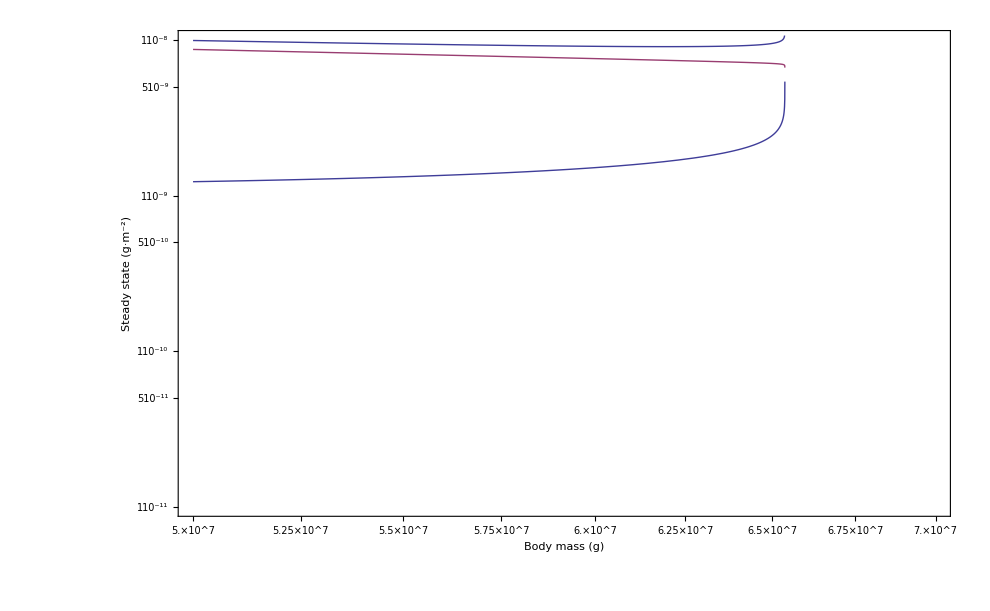

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{5*10^7,7*10^7},{10^-11,10^(-8)}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],
LogLogPlot[{dimH/M,dimF/M},{M,5*10^7,7*10^7},PlotStyle->{ColorData[97,2],ColorData[97,3]}],
LogLogPlot[(dimH/M)+(dimF/M),{M,5*10^7,7*10^7},PlotStyle->ColorData[97,3]]
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
ListLogLogPlot[data]
}]
```

```mathematica
B0
```

0.047

ColorData::notent: 97 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

Graphics::gprim: ColorData[97, 2] was encountered where a Graphics primitive or directive was expected.

Graphics::gprim: ColorData[97, 3] was encountered where a Graphics primitive or directive was expected.

ColorData::notent: 97 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData :: notent will be suppressed during this calculation.

Graphics::gprim: ColorData[97, 3] was encountered where a Graphics primitive or directive was expected.

General::stop: Further output of Graphics :: gprim will be suppressed during this calculation.

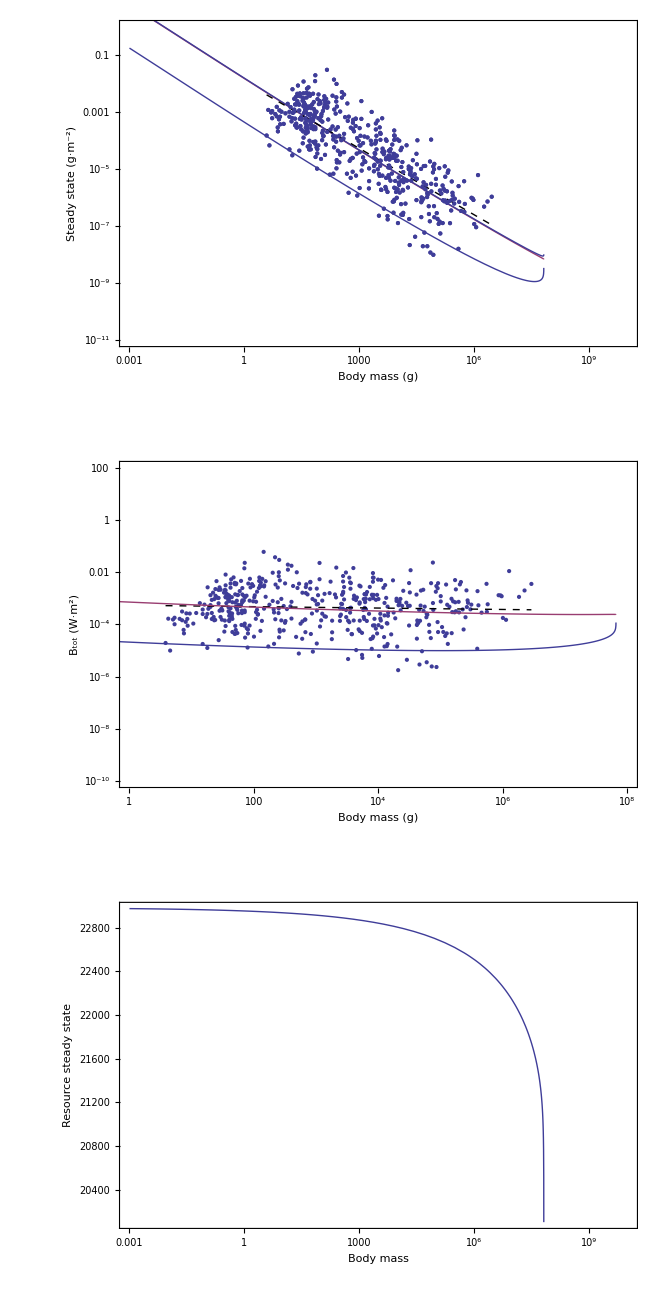

```mathematica
Cplot=GraphicsGrid[{{
Show[{
ListLogLogPlot[data,PlotRange->{{.001,10^10},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],
LogLogPlot[{dimH/M,dimF/M},{M,.001,10^10},PlotStyle->{ColorData[97,2],ColorData[97,3]}],
LogLogPlot[(dimH/M)+(dimF/M),{M,.001,10^10},PlotStyle->ColorData[97,3]]
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
ListLogLogPlot[data]
}]
},{
Show[{
ListLogLogPlot[Table[{data[[i]][[1]],data[[i]][[2]]*(data[[i]][[1]])^(3/4)*B0},{i,Length[data]}],PlotRange->{{1,10^8},{10^-10,100}},Frame->True,FrameLabel->{"Body mass (g)","B_tot (W·m^2)"}],
LogLogPlot[0.0115643*M^(-0.776818)*M^(3/4)*B0,{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
LogLogPlot[{dimH/M*M^(3/4)*B0,dimF/M*M^(3/4)*B0},{M,.001,10^10},Frame->True,FrameLabel->{"Body mass (g)","B_tot"},PlotStyle->{ColorData[97,2],ColorData[97,3]}]}]
},{
LogLinearPlot[dimR,{M,.001,10^10},Frame->True,PlotRange->All,FrameLabel->{"Body mass","Resource steady state"}]
}}]
```

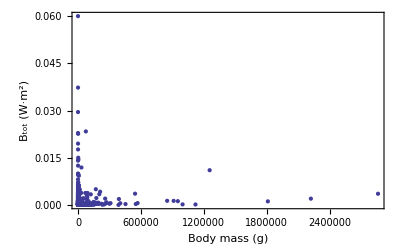

```mathematica
ListPlot[Table[{data[[i]][[1]],data[[i]][[2]]*(data[[i]][[1]])^(3/4)*B0},{i,Length[data]}],PlotRange->All,Frame->True,FrameLabel->{"Body mass (g)","B_tot (W·m^2)"}]
```

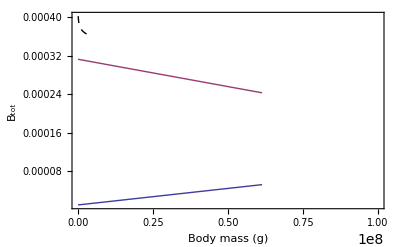

```mathematica
Show[{
Plot[{dimH/M*M^(3/4)*B0,dimF/M*M^(3/4)*B0},{M,.001,10^12},Frame->True,FrameLabel->{"Body mass (g)","B_tot"},PlotRange->{{0,10^8},All}],
Plot[0.0115643*M^(-0.776818)*M^(3/4)*B0,{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]]}]
```

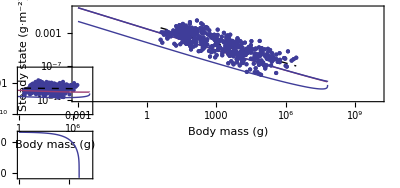

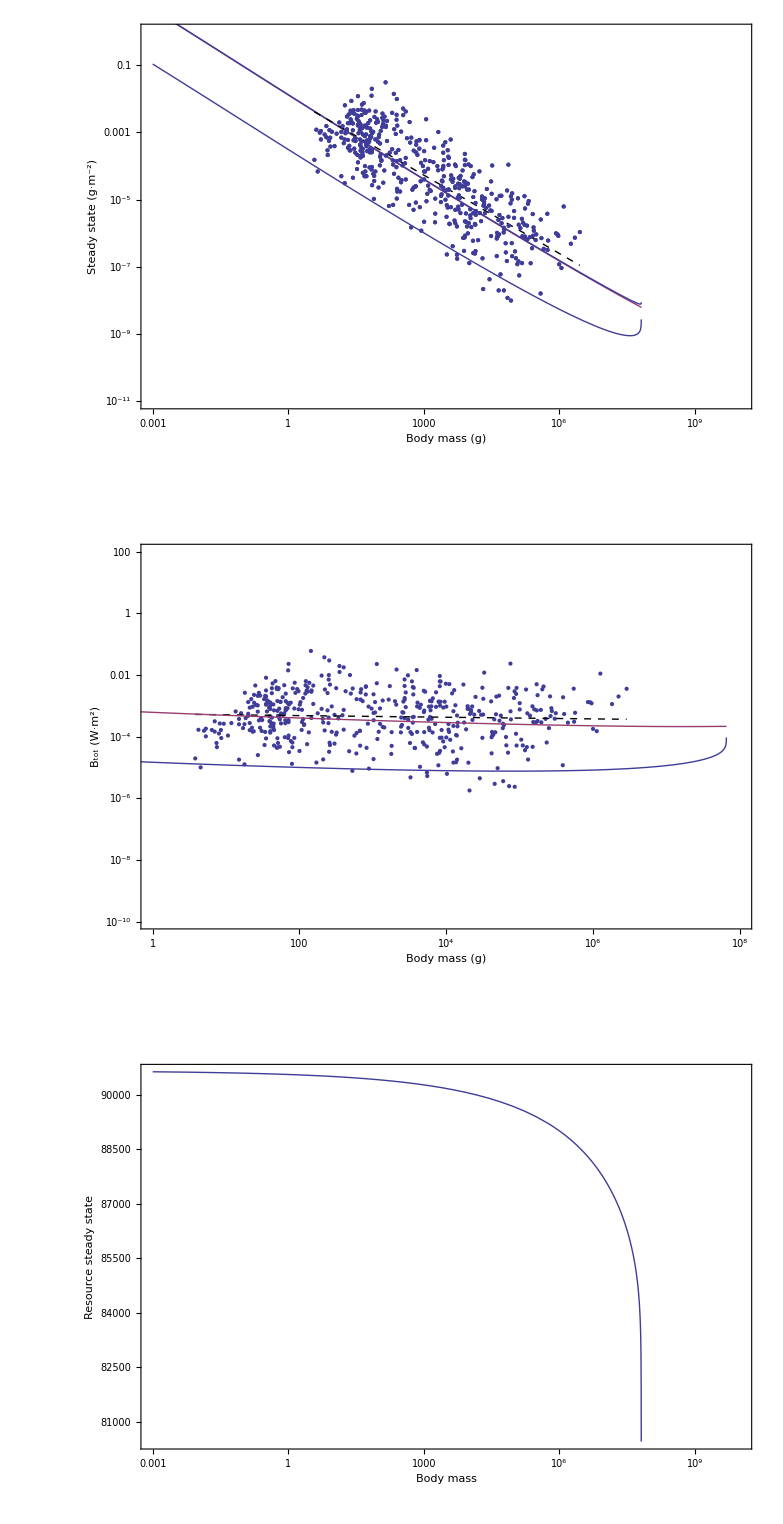

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf"}],Cplot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf

```mathematica
NIntegrate[(1/M)*(dimF/M*M^(3/4)*B0),{M,10^3,10^5}]
```

0.000132489

```mathematica
FindMaximum[Re[HFM[[1]]],M]
```

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{1.59227,{M→6.53794×10^7}}

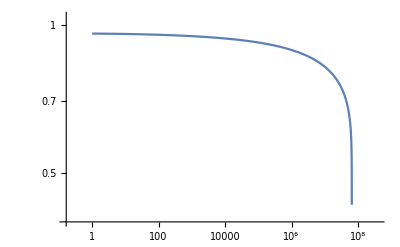

```mathematica
LogLogPlot[StarRates[[1]],{M,1,10^9},PlotRange->All]
```

```mathematica
FindMinimum[Re[StarRates[[1]]],M]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{0.255557,{M→6.53794×10^7}}